```mathematica
"tempRhoLogPlot";
```

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
```

```mathematica
SetDirectory@NotebookDirectory[];
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
HideText["Basic setup"]
```

Basic setup

```mathematica
<<MaTeX`
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\xelatex.exe"];*)
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\pdflatex.exe"];*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,nicefrac,esint,siunitx,bm}"}(*,"Magnification"->1.2*)];
MyTeX[x_]:=HideText[MaTeX[x]];
HideText["MaTeX Loaded"]
```

MaTeX Loaded

```mathematica
(*<<ErrorBarPlots`*)
```

```mathematica
omarker=Graphics[{Thickness[.2],Circle[]}];
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListPlot]))/.Directive[x_,__]:>x);
HideText["omarker & colors"]
```

omarker & colors

```mathematica
tempRhoRaw=Import["data.xlsx"]⟦1⟧⟦3;;24,{6,14}⟧;
HideText["tempRhoRaw; temp in Celsius, rho in Ohm.cm"]
```

tempRhoRaw; temp in Celsius, rho in Ohm.cm

```mathematica
logRhoDat={(1000./(#1+273.15)),Log[#2]}&@@@tempRhoRaw;
```

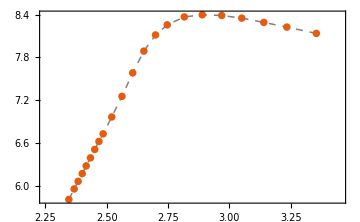

tempRhoLog.pdf

```mathematica
tempRhoLog=Show[ListLinePlot[logRhoDat,
PlotTheme->"Scientific",
(*PlotMarkers->{omarker,.012},*)
PlotStyle->{Dashed,Thickness[.003],Gray},
PlotRange->{{2.25,3.45},Automatic},
PlotRangePadding->{{0,0},{.5,.5}},
ImagePadding->{{48,48},{25,36}},
ImageSize->Medium,
GridLines->None],
ListPlot[logRhoDat,
PlotStyle->{PointSize[.015],colors⟦1⟧}],
Epilog->Join[
(Inset[Evaluate@MaTeX[#1,
Magnification->.9],#2]&)@@@{
{"\\frac{\\SI{e3}{\\K}}{T}",Scaled[{1.08,0}]},
{"\\ln\\frac{\\rho}{\\si{\\ohm\\cdot\\cm}}",Scaled[{0,1.12}]}
},
Inset[
Graphics[{EdgeForm[Dotted],Opacity[0],
Rectangle@@(Scaled/@#1)}],
Scaled[#2]]&@@@{
{{{0,0},{.45,.15}},{.975,1.28}}
}],
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@tempRhoLog
AutoCollapse[];
```

```mathematica
tempHallRaw=Import["data.xlsx"]⟦1⟧⟦3;;24,{6,23}⟧;
HideText["tempHallRaw; temp in Celsius, hall in 10^4.cm^3.C"]
```

tempHallRaw; temp in Celsius, hall in 10^4.cm^3.C

```mathematica
logHallDatPlus={(1000./(#1+273.15)),Log[Abs[#2]]}&@@@(Select[#⟦2⟧>0&]@tempHallRaw);
LogHallDatNeg={(1000./(#1+273.15)),Log[Abs[#2]]}&@@@(Select[#⟦2⟧<0&]@tempHallRaw);
HideText@"logHallDatPlus & Neg"
```

logHallDatPlus & Neg

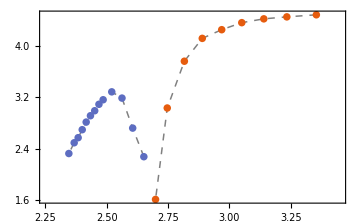

tempHallLog.pdf

```mathematica
tempHallLog=Show[
ListLinePlot[
Evaluate[Select[
!MemberQ[tempHallRaw⟦{5,11,13}⟧,#]&]/@{logHallDatPlus,LogHallDatNeg}],
PlotTheme->"Scientific",
(*PlotMarkers->{omarker,.012},*)
PlotStyle->Directive[Dashed,Thickness[.003],Gray],
PlotRange->{{2.25,3.45},Automatic},
PlotRangePadding->{{0,0},{.5,.5}},
ImagePadding->{{48,48},{25,36}},
ImageSize->Medium,
GridLines->None],
ListPlot[{logHallDatPlus,LogHallDatNeg},
PlotStyle->Evaluate[Directive[PointSize[.015],#]&/@colors],
PlotLegends->Placed[HoldForm@Evaluate@SwatchLegend[colors,
MaTeX[#,Magnification->.8]&/@{
"R_H > 0","R_H < 0"},
LegendMarkerSize->5],
{.8,.28}]
],
Epilog->(Inset[Evaluate@MaTeX[#1,
Magnification->.9],#2]&)@@@{
{"\\frac{\\SI{e3}{\\K}}{T}",Scaled[{1.08,0}]},
{"\\ln\\frac{|R_H|}{\\SI{e4}{\\cm^3.\\coulomb}}",Scaled[{0,1.12}]}
},
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@tempHallLog
AutoCollapse[];
```